# Assignment 11

Karim Sobh
201700836

## Fig 10.12

75.7631

5.23567

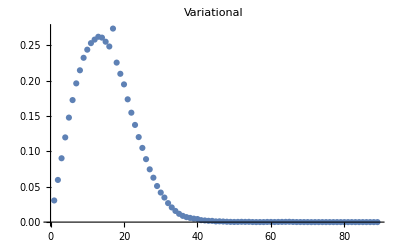

```mathematica
dr = 0.05; rMin = 0.6;rMax = 5.0;
r = Range[rMin,rMax,dr]; lr = Length[r];
phi = Table[0.0,{i,lr}];
LL=Position[r,1.0][[1,1]];
RR=Position[r,4.0][[1,1]];
phi[[LL;;RR]]=0.5;
phi = phi/(√(phi.phi dr)); (* normalization *)
pot = r^4; (* Discrete potential *)
hm = Array[0 &, {lr,lr}];
d2 = 1.0/dr^2;
d1 = -0.50/dr^2;
hm[[1,1]] = pot[[1]] + d2;
hm[[1,2]] =  d1;
hm[[lr,lr]] = pot[[lr]] + d2;
hm[[lr,lr-1]] =  d1;
Do[
	hm[[i,i-1]] = d1;hm[[i,i+1]] = d1;hm[[i,i]] = pot[[i]] + d2,
	{i,2,lr-1}]
hm//MatrixForm;
engOld = dr phi.hm.phi
Do[
	RanI =RandomInteger[{1,lr}];
	phiTry = phi;
	phiTry[[RanI]] = phiTry[[RanI]]+ RandomReal[{-0.2,0.2}];
	phiTry = phiTry/(√(phiTry.phiTry dr));
	engNew =dr phiTry.hm.phiTry; 
	If[engNew < engOld,phi =phiTry; engOld = engNew],
	{j,100000}]
engOld
ListPlot[phiTry*Sqrt[dr],PlotLabel->"Variational"]
```

4.69676

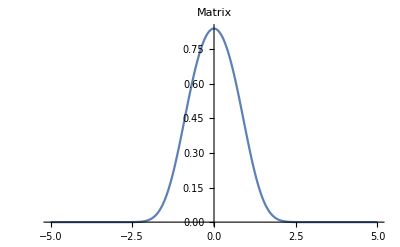

```mathematica
dr =2.0^-8; rMax=5.0;
r = Range[-rMax,rMax,dr];
lr = Length[r];
pot = r^4;
d1 =-1.0/(2.0 dr^2);
d2 = 1.0/(dr^2);
hm = Array[0 &, {lr,lr}];
hm[[1,1]] = pot[[1]] + d2;
hm[[1,2]] =  d1;
hm[[lr,lr]] = pot[[lr]] + d2;
hm[[lr,lr-1]] =  d1;
Do[
	hm[[i,i-1]] = d1;hm[[i,i+1]] = d1;hm[[i,i]] = pot[[i]] + d2,
{i,2,lr-1}]
ig=Position[Eigenvalues[hm],Min[Eigenvalues[hm]]][[1,1]];
en =Sort[Eigenvalues[hm]];
Psii=Eigenvectors[hm];
psig=Psii[[ig]];
length=Sqrt[Sum[psig[[i]]^2 *dr,{i,1,lr}]];
data=Table[{r[[i]],psig[[i]]/length},{i,1,lr}];
en[[3]]
ListPlot[data, Joined->True,PlotLabel->"Matrix"]
```

## Figure 10.14

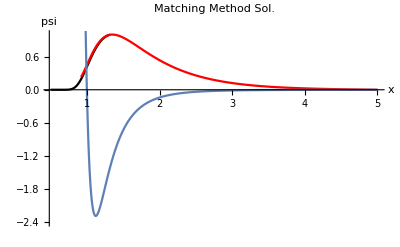

-1.19337

```mathematica
dx = 0.01; xMin = 0.5;xMax = 5.0; 
x = Range[xMin,xMax,dx]; lx = Length[x];
eng =-3; (* first guess for E *)

dE = .4; (* first guess for dE *) 

vLJ[x_,ϵ_,σ_]:= 4 ϵ ((σ/x)^12-(σ/x)^6);
v = vLJ[x,8.0,1.0]; 
iMin = Position[v,Min[v]][[1,1]]; 

iOveLLap = 20; 
 
psiL = Table[0.0, {i,iMin + iOveLLap}]; 
lL = Length[psiL];
psiR = Table[0.0, {i,iMin - iOveLLap,lx}]; 
lR = Length[psiR];


psiL[[1]] = -0.0001 dx; psiR[[1]] =psiL[[1]]; 


Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[i-1]])psiR[[i-1]] dx^2  
,{i,3,lR}];
psiR = Reverse[psiR]; 
psiL = psiL psiR[[iOveLLap]]/psiL[[iMin]]; 


sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOveLLap+1]] -  psiR[[iOveLLap-1]];last=sR-sL;
While[Abs[dE]>0.000001,psiL = Table[0.0, {i,iMin + iOveLLap}]; 
lL = Length[psiL];
psiR = Table[0.0, {i,iMin - iOveLLap,lx}]; 
lR = Length[psiR];


psiL[[1]] = -0.0001 dx; psiR[[1]] =psiL[[1]]; 


Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}];
psiR = Reverse[psiR]; 
psiL = psiL psiR[[iOveLLap]]/psiL[[iMin]]; 


sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOveLLap+1]] -  psiR[[iOveLLap-1]];new=sR-sL;If[Sign[last]≠ Sign[new],dE=-dE/2];eng=eng+dE;last=new];length=Sqrt[Sum[psiL[[i]]^2 *dx,{i,1,lL}]+Sum[psiR[[i]]^2 *dx,{i,1,lR}]];
xpsiL = Table[{x[[i]], psiL[[i]]/length},{i,lL}];
xpsiR = Table[{x[[i+lx-lR]], psiR[[i]]/length},{i,lR}]; 
p1 = ListPlot[xpsiL, PlotStyle->Black, Joined->True,PlotRange->{All,{-2.4,1}}];  p2 = ListPlot[xpsiR,PlotStyle->Red, Joined->True,PlotRange->{All,{-2.4,1}}]; p3=Plot[vLJ[x,8.0,1.0]/3.5,{x,0.5,5},PlotRange->All,AxesLabel->{"x","V(x)"}];
Show[p1,p2,p3,PlotRange-> {All,{-2.4,1}},AxesLabel-> {"x","psi"},PlotLabel->"Matching Method Sol."]
eng
```

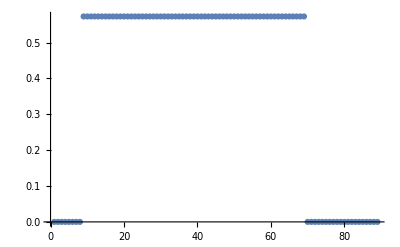

-0.886481

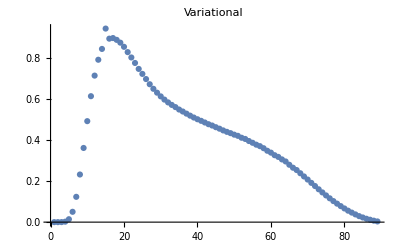

```mathematica
dx = 0.05; xMin = 0.6;xMax = 5.0; 
x = Range[xMin,xMax,dx]; lx = Length[x];
phi = Table[0.0,{i,lx}];
Do[
If[x[[i]]>= 1.0 && x[[i]]<= 4.0, phi[[i]] = 0.50]
,{i,lx}];
phi = phi/(√(phi.phi dx)); (* normalization *)

ListPlot[phi]
vLJ[x_,ϵ_,σ_]:= 4 ϵ ((σ/x)^12-(σ/x)^6);
pot = vLJ[x,8.0,1.0]; (* Discrete potential *)
hm = Array[0 &, {lx,lx}];
d2 = 1.0/dx^2;
d1 = -0.50/dx^2;
hm[[1,1]] = pot[[1]] + d2;
hm[[1,2]] =  d1;
hm[[lx,lx]] = pot[[lx]] + d2;
hm[[lx,lx-1]] =  d1;
Do[
hm[[i,i-1]] = d1;hm[[i,i+1]] = d1;hm[[i,i]] = pot[[i]] + d2,
{i,2,lx-1}]
hm//MatrixForm;

engOld = dx phi.hm.phi;

Do[
RanI =RandomInteger[{1,lx}];
phiTry = phi;
phiTry[[RanI]] = phiTry[[RanI]]+ RandomReal[{-0.2,0.2}];
phiTry = phiTry/(√(phiTry.phiTry dx));
engNew =dx phiTry.hm.phiTry; 
If[engNew < engOld,phi =phiTry; engOld = engNew],
{j,1000000}]
engOld
ListPlot[phiTry,PlotLabel->"Variational"]
```